# Homework assignment 7

Kyle McGraw <kmcgraw@caltech.edu>

```mathematica
SetDirectory[NotebookDirectory[]];
Get["CRNSimulator.m"]
Get["CRNSimulatorSSA.m"]
```

```mathematica
WeightedTrajectory[trajectory_,speciesIndex_,OptionsPattern[{Normalized->False}]]:=WeightedData[
Floor[#[[speciesIndex]]]&/@Drop[trajectory["Values"],-1],
Differences[trajectory["Times"]]/If[OptionValue[Normalized],Last[trajectory["Times"]],1]
]
```

## Part 1: The mixture CRN.

(a) Find parameters such that the steady state maintains X with a mean count of 100 and a standard deviation of 10.  Exactly.  Justify your choices.  Plot a sample trajectory (i.e. counts of A, B, and X as a function of time) and a histogram of counts of X (bin size 1, normalized such that the value for a bin is the probability of that count in the sample).  The sample of course is only a sample and won’t exactly match the true steady-state probabilities for this CRN.

```mathematica
Clear[mixture,balance,message,A,B,antiX,X,Y,P]
```

```mathematica
mixture[k1_,k2_,p1_,p2_]:=Join[
{rxn[A,A+X,k1],rxn[B,B+X,k2]},
{rxn[A+X,A,1],rxn[B+X,B,1]},
{rxn[0,A,p1],rxn[0,B,p2],rxn[A+B,A,1000],rxn[A+B,B,1000],rxn[2A,A,1000],rxn[2B,B,1000]}
]
```

```mathematica
mix=mixture[100,100,1000,1000]
```

{  A⟶^100A+X,  B⟶^100B+X,  A+X⟶^1A,  B+X⟶^1B,  0⟶^1000A,  0⟶^1000B,  A+B⟶^1000A,  A+B⟶^1000B,  2 A⟶^1000A,  2 B⟶^1000B}

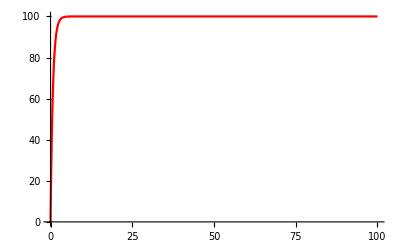

```mathematica
tmax=100;
sol=SimulateRxnsys[mix,tmax];Plot[Evaluate[X[t]/.sol],{t,0,tmax},PlotRange->{0,All},PlotStyle->{{Red}}]
```

```mathematica
tmax=300;
trajectory=SimulateRxnsysSSA[mix,tmax];
ListLinePlot[trajectory,PlotRange->{0,All},
PlotLegends->SpeciesInRxnsys[mix]]
```

-Graphics-

```mathematica
data=WeightedTrajectory[trajectory,3,Normalized->True];
Histogram[data,{1},PlotLabel->"Fraction of time spent in state with given count",Epilog->Inset[TableForm[{{"Mean:",Mean[data]},{"SD:",StandardDeviation[data]}}],{Center,Center},{Center,Center}]]
```

-Graphics-

To keep the counts of X at a mean of 100, we want to have the k1 and k2 parameters to add up to 200. To make the standard deviation equal to 10, we want the values of k1 and k2 to both be equal to 100 for root 100 = 10 noise.

(b) Find parameters such that the steady state maintains a unimodal distribution (one peak) with mean 100 and a standard deviation of roughly 25.  Plot a sample trajectory and corresponding sampled distribution.  Justify your parameters with an informal argument.

```mathematica
mix2=mixture[175,25,10,10]
```

{  A⟶^175A+X,  B⟶^25B+X,  A+X⟶^1A,  B+X⟶^1B,  0⟶^10A,  0⟶^10B,  A+B⟶^1000A,  A+B⟶^1000B,  2 A⟶^1000A,  2 B⟶^1000B}

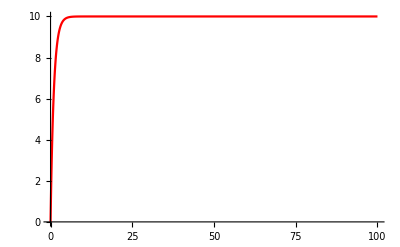

```mathematica
tmax=100;
sol=SimulateRxnsys[mix2,tmax];Plot[Evaluate[X[t]/.sol],{t,0,tmax},PlotRange->{0,All},PlotStyle->{{Red}}]
```

```mathematica
tmax=300;
trajectory2=SimulateRxnsysSSA[mix2,tmax];
ListLinePlot[trajectory2,PlotRange->{0,All},
PlotLegends->SpeciesInRxnsys[mix2]]
```

-Graphics-

```mathematica
data2=WeightedTrajectory[trajectory2,3,Normalized->True];
Histogram[data2,{1},PlotLabel->"Fraction of time spent in state with given count",Epilog->Inset[TableForm[{{"Mean:",Mean[data2]},{"SD:",StandardDeviation[data2]}}],{Center,Center},{Center,Center}]]
```

-Graphics-

To keep the counts of X at a mean of 100, we want to have the k1 and k2 parameters to add up to 200. To make the standard deviation larger than 10, we want the values of k1 and k2 to be inequal and can set them to 175 and  25. With large p1 and p2, we get the same histogram as part a, but if we reduce the p1 and p2 then the system will stay in the A and B states for longer and we will get larger spreads. Setting p1 and p2 to both be 10, we get more time in each state than in part a for a larger spread of values but still enough fluctuation between states that we have a single peak.

(c) Find parameters such that the steady state maintains a bimodal distribution (two peaks) with means 100 and 49 and with respective standard deviations of roughly 10 and 7.  (By standard deviation of a mode, we consider just those points that are closer to one peak rather than the other.)

```mathematica
mix3=mixture[100,49,0.01,0.01]
```

{  A⟶^100A+X,  B⟶^49B+X,  A+X⟶^1A,  B+X⟶^1B,  0⟶^0.01A,  0⟶^0.01B,  A+B⟶^1000A,  A+B⟶^1000B,  2 A⟶^1000A,  2 B⟶^1000B}

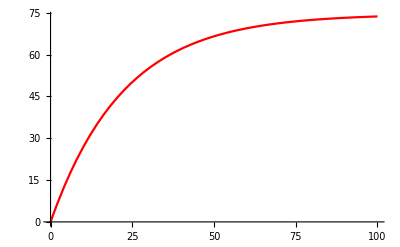

```mathematica
tmax=100;
sol=SimulateRxnsys[mix3,tmax];Plot[Evaluate[X[t]/.sol],{t,0,tmax},PlotRange->{0,All},PlotStyle->{{Red}}]
```

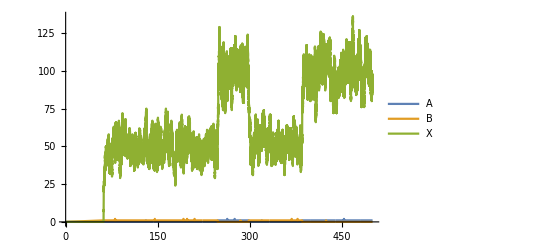

```mathematica
tmax=500;
trajectory3=SimulateRxnsysSSA[mix3,tmax];
ListLinePlot[trajectory3,PlotRange->{0,All},
PlotLegends->SpeciesInRxnsys[mix3]]
```

```mathematica
data3=WeightedTrajectory[trajectory3,3,Normalized->True];
Histogram[data3,{1},PlotLabel->"Fraction of time spent in state with given count",Epilog->Inset[TableForm[{{"Mean:",Mean[data3]},{"SD:",StandardDeviation[data3]}}],{Center,Center},{Center,Center}]]
```

-Graphics-

```mathematica
partition[wd_WeightedData,separator_]:=Module[{d=wd["InputData"],w=wd["Weights"],i1,i2},i1=Flatten[Position[d,_?((#<separator)&)]];
i2=Flatten[Position[d,_?((#≥separator)&)]];
{WeightedData[d[[i1]],w[[i1]]],WeightedData[d[[i2]],w[[i2]]]}]
```

```mathematica
{partition1,partition2}=partition[partition[data3,1][[2]],72];
```

```mathematica
Histogram[partition1,{1},PlotLabel->"Fraction of time spent in state with given count",Epilog->Inset[TableForm[{{"Mean:",Mean[partition1]},{"SD:",StandardDeviation[partition1]}}],{Center,Center},{Center,Center}]]
```

-Graphics-

```mathematica
Histogram[partition2,{1},PlotLabel->"Fraction of time spent in state with given count",Epilog->Inset[TableForm[{{"Mean:",Mean[partition2]},{"SD:",StandardDeviation[partition2]}}],{Center,Center},{Center,Center}]]
```

-Graphics-

To get means of 100 and 49, we want to have the k1 and k2 parameters to be 100 and 49, respectively. To get two different peaks, we want to reduce p1 and p2 even further then part b so the system will stay in the A and B states for longer and we will two spreads around each of the means. Setting p1 and p2 to both be 0.01, we get extended periods of time fluctuating around each state for a bimodal distribution (also get an extended time in the initial 0 state that I remove for the graphing). Standard deviations work out because this system has root-N noise.

## Part 2: The balance CRN.

A common misconception is that stochastic CRNs inevitably exhibit “root-N” noise, i.e. that if the mean count of some species is N, then its standard deviation will be √N, or perhaps more.  This is indeed often the case, as in the CRN of Part 1.  However, the noise level in a stochastic CRN can also be arbitrarily small.  For example, consider the RESTORE gate for digital logic circuits with deterministic bulk CRNs.  A long chain of RESTORE gates will very sensitively distinguish between an input concentration being above or below 0.5 nM (if we chose units where “zero” is 0 nM and “one” is 1 nM).  Might this same CRN in a finite volume of 100 V_0 (where V_0=1.66 fL) sensitively  distinguish between an input of 0.49 nM (i.e. 49 molecules) vs an input of 0.51 nM (i.e. 51 molecules)?  And if so, could the output of the chain be used to slowly create or destroy input, so as to stabilize the input at precisely a count of 50 molecules ±1?   Don’t answer that, it’s a rhetorical question, and a bit more subtle than it might seem.  Instead, we will examine a conceptually related CRN that is easier to analyze and faster to simulate.

(a) Consider the balance CRN with act=0 and initial #X=N+1, #A[0]=1, all other species absent.  N and K each may be any positive integer.  What is steady-state probability ratio Prob(#A[K]==1)/Prob(#A[-K]==1) ? For #X=N-1?  For #X=N?
When we have act = 0, X stays at N+1. Since we have N+1 X molecules and the transitions towards A[K] go at rate 1/N, this will tend towards A[K] so the probability ratio will be >1; the rate between each state towards A[K] is N+1/N and the rate in the other direction is 1, so we get a probability of n+1/2n+1 of increasing and n/2n+1 of decreasing.

Similarly, with N-1 X molecules, we will be going towards A[K] at a slower rate than towards A[-K] so will have a probability ration of <1; the rate between each state towards A[K] is N-1/N and the rate in the other direction is 1, so we get a probability of n-1/2n-1 of increasing and n/2n-1 of decreasing.

When there are exactly N X molecules the rates in both direction will be identical, so the probability ratio will be exactly 1.

```mathematica
balance[K_,N_,act_]:=Flatten[Join[
Table[rxn[A[i]+X,A[i+1]+X,1/N],{i,-K,K-1}],
Table[rxn[A[i+1],A[i],1],{i,-K,K-1}],
{rxn[A[-K],A[0]+X,act],rxn[A[K],A[0]+antiX,act],rxn[X+antiX,0,act]},
{conc[A[0],1],conc[X,N+1]}
]]
```

```mathematica
bal=balance[5,3,0]
```

{  X+A[-5]⟶^(1/3)X+A[-4],  X+A[-4]⟶^(1/3)X+A[-3],  X+A[-3]⟶^(1/3)X+A[-2],  X+A[-2]⟶^(1/3)X+A[-1],  X+A[-1]⟶^(1/3)X+A[0],  X+A[0]⟶^(1/3)X+A[1],  X+A[1]⟶^(1/3)X+A[2],  X+A[2]⟶^(1/3)X+A[3],  X+A[3]⟶^(1/3)X+A[4],  X+A[4]⟶^(1/3)X+A[5],  A[-4]⟶^1A[-5],  A[-3]⟶^1A[-4],  A[-2]⟶^1A[-3],  A[-1]⟶^1A[-2],  A[0]⟶^1A[-1],  A[1]⟶^1A[0],  A[2]⟶^1A[1],  A[3]⟶^1A[2],  A[4]⟶^1A[3],  A[5]⟶^1A[4],  A[-5]⟶^0X+A[0],  A[5]⟶^0antiX+A[0],  antiX+X⟶^00,conc[A[0],1],conc[X,4]}

```mathematica
tmax=100000;
traj=SimulateRxnsysSSA[bal,tmax];
```

```mathematica
SpeciesInRxnsys[bal]
```

{antiX,X,A[-5],A[-4],A[-3],A[-2],A[-1],A[0],A[1],A[2],A[3],A[4],A[5]}

```mathematica
Mean[traj["Values"][[All,Length[SpeciesInRxnsys[bal]]]]]/Mean[traj["Values"][[All,3]]]
```

25976/2145

```mathematica
balance[K_,N_,act_]:=Flatten[Join[
Table[rxn[A[i]+X,A[i+1]+X,1/N],{i,-K,K-1}],
Table[rxn[A[i+1],A[i],1],{i,-K,K-1}],
{rxn[A[-K],A[0]+X,act],rxn[A[K],A[0]+antiX,act],rxn[X+antiX,0,act]},
{conc[A[0],1],conc[X,N-1]}
]]
```

```mathematica
bal=balance[5,3,0]
```

{  X+A[-5]⟶^(1/3)X+A[-4],  X+A[-4]⟶^(1/3)X+A[-3],  X+A[-3]⟶^(1/3)X+A[-2],  X+A[-2]⟶^(1/3)X+A[-1],  X+A[-1]⟶^(1/3)X+A[0],  X+A[0]⟶^(1/3)X+A[1],  X+A[1]⟶^(1/3)X+A[2],  X+A[2]⟶^(1/3)X+A[3],  X+A[3]⟶^(1/3)X+A[4],  X+A[4]⟶^(1/3)X+A[5],  A[-4]⟶^1A[-5],  A[-3]⟶^1A[-4],  A[-2]⟶^1A[-3],  A[-1]⟶^1A[-2],  A[0]⟶^1A[-1],  A[1]⟶^1A[0],  A[2]⟶^1A[1],  A[3]⟶^1A[2],  A[4]⟶^1A[3],  A[5]⟶^1A[4],  A[-5]⟶^0X+A[0],  A[5]⟶^0antiX+A[0],  antiX+X⟶^00,conc[A[0],1],conc[X,2]}

```mathematica
tmax=100000;
traj=SimulateRxnsysSSA[bal,tmax];
```

```mathematica
SpeciesInRxnsys[bal]
```

{antiX,X,A[-5],A[-4],A[-3],A[-2],A[-1],A[0],A[1],A[2],A[3],A[4],A[5]}

```mathematica
Mean[traj["Values"][[All,Length[SpeciesInRxnsys[bal]]]]]/Mean[traj["Values"][[All,3]]]
```

53/2062

```mathematica
balance[K_,N_,act_]:=Flatten[Join[
Table[rxn[A[i]+X,A[i+1]+X,1/N],{i,-K,K-1}],
Table[rxn[A[i+1],A[i],1],{i,-K,K-1}],
{rxn[A[-K],A[0]+X,act],rxn[A[K],A[0]+antiX,act],rxn[X+antiX,0,act]},
{conc[A[0],1],conc[X,N]}
]]
```

```mathematica
bal=balance[5,3,0]
```

{  X+A[-5]⟶^(1/3)X+A[-4],  X+A[-4]⟶^(1/3)X+A[-3],  X+A[-3]⟶^(1/3)X+A[-2],  X+A[-2]⟶^(1/3)X+A[-1],  X+A[-1]⟶^(1/3)X+A[0],  X+A[0]⟶^(1/3)X+A[1],  X+A[1]⟶^(1/3)X+A[2],  X+A[2]⟶^(1/3)X+A[3],  X+A[3]⟶^(1/3)X+A[4],  X+A[4]⟶^(1/3)X+A[5],  A[-4]⟶^1A[-5],  A[-3]⟶^1A[-4],  A[-2]⟶^1A[-3],  A[-1]⟶^1A[-2],  A[0]⟶^1A[-1],  A[1]⟶^1A[0],  A[2]⟶^1A[1],  A[3]⟶^1A[2],  A[4]⟶^1A[3],  A[5]⟶^1A[4],  A[-5]⟶^0X+A[0],  A[5]⟶^0antiX+A[0],  antiX+X⟶^00,conc[A[0],1],conc[X,3]}

```mathematica
tmax=100000;
traj=SimulateRxnsysSSA[bal,tmax];
```

```mathematica
SpeciesInRxnsys[bal]
```

{antiX,X,A[-5],A[-4],A[-3],A[-2],A[-1],A[0],A[1],A[2],A[3],A[4],A[5]}

```mathematica
Mean[traj["Values"][[All,Length[SpeciesInRxnsys[bal]]]]]/Mean[traj["Values"][[All,3]]]
```

9218/9143

(b) In the three cases above, where at any given time there is only one A[i] molecule present, let i(t) indicate which species is currently present.  Then i either does an unbiased random walk, or it does a biased random walk that on average drifts up toward K or drifts down toward -K.  For large K, give simple formulas that approximate how long it takes before i first reaches -K or K, for each of the three cases.
We expect to move right once in time 1/p-q where p is the probability of moving right and q is the probability of moving left (same for going opposite direction) (formula from page 5 on passage times of random walk from http://www2.math.uu.se/~sea/kurser/stokprocmn1/slumpvandring_eng.pdf).

For the X = N+1 case, we have a higher probability of moving right so on average drift up toward K. Since we have a probability of n+1/2n+1 of increasing and n/2n+1 of decreasing, the expected time to move a step right would be 1/(n+1/2n+1 - n/2n+1) = 2n+1. The expected time to reach K then would be K*(2n+1).

For the X = N-1 case, we have a higher probability of moving left so on average drift down toward -K. Since we have a probability of n-1/2n-1 of increasing and n/2n-1 of decreasing, the expected time to move a step left would be 1/(n/2n-1 - n-1/2n-1) = 2n-1. The expected time to reach -K then would be K*(2n-1).

When there are exactly N X molecules the rates in both direction will be identical, so expected time is infinity.

(c) Justified by your arguments above, choose K, N, act so that the steady-state distribution for X has mean 50 and standard deviation roughly 1 or less. Do a simulation long enough to witness at least 25 adjustments of X after reaching steady-state.

```mathematica
balance[K_,N_,act_]:=Flatten[Join[
Table[rxn[A[i]+X,A[i+1]+X,1/N],{i,-K,K-1}],
Table[rxn[A[i+1],A[i],1],{i,-K,K-1}],
{rxn[A[-K],A[0]+X,act],rxn[A[K],A[0]+antiX,act],rxn[X+antiX,0,act]},
{conc[A[0],1],conc[X,N]}
]]
```

```mathematica
bal=balance[15,50,1000];
```

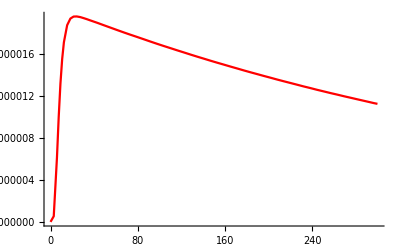

```mathematica
tmax=300;
sol=SimulateRxnsys[bal,tmax];Plot[Evaluate[X[t]/.sol],{t,0,tmax},PlotRange->{0,All},PlotStyle->{{Red}}]
```

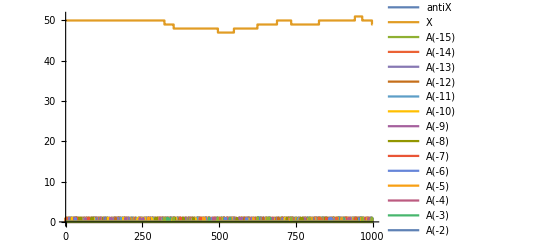

```mathematica
tmax=1000;
trajectory=SimulateRxnsysSSA[bal,tmax];
ListLinePlot[trajectory,PlotRange->{0,All},
PlotLegends->SpeciesInRxnsys[bal]]
```

```mathematica
data=WeightedTrajectory[trajectory,2,Normalized->True];
Histogram[data,{1},PlotLabel->"Fraction of time spent in state with given count",Epilog->Inset[TableForm[{{"Mean:",Mean[data]},{"SD:",StandardDeviation[data]}}],{Center,Center},{Center,Center}]]
```

-Graphics-

## Part 3: The message CRN.

Not all that glitters is gold, and not all that scatters is noise.  Run crn3 with tmax=200,000 and plot the trajectory as a function of time as well as a 2D density histogram showing what fraction of the time is spent in each (X,Y) state.  The following command will display non-visited states in trajectory as white as well as states that are very rarely visited, while the most-visited state will be black:
	DensityHistogram[WeightedTrajectory[trajectory,{1,2}],{1},ColorFunction→Function[{d},GrayLevel[1-d]]]
Explain how crn3 works.  In particular, comment on what each type of reaction is doing, conceptually, and give some justification for why the rate constants are chosen as they are.  It will be helpful to imagine possible failure modes, and to estimate the frequency with which they happen.

We have 5 different types of reactions. The first type of reaction is a reversible reaction that creates a chemical representing each pixel at a very slow rate; the reverse of this reaction goes at a slow but slightly quicker rate. This type of reaction is so that all pixels will stay near 0 but will also spend time with some of their chemical species present; this is because we want all the pixels to exist for a non-zero amount of time but ideally only one type exists at a time. The second type of reaction for each pixel chemical present, we destroy 1 X but requiring the pixel’s X coord of X’s ((p.x-1)*X -> p.x*X). The fourth type of reaction for each pixel chemical present, we create 1 X at rate 1. These two sets of reactions are done to put the state of the system at the X coordinate of the pixel that is present; it does this by each time a pixel chemical is present putting the reactions creating and destroying X such that X stays at a steady state at the value of the X coordinate of the pixel. The third and fifth types of reaction do the same but for the Y coordinates.

```mathematica
message[pixels_,epsilon_] := Module[{S,N,a},
S = Length[pixels]; N = Max[Flatten[pixels]]; a = S/Sqrt[2*epsilon];
Flatten[{
Table[revrxn[0,P[i],epsilon/N/a,epsilon/N],{i,S}],
Table[rxn[P[i]+(pixels[[i,1]]+1) X, P[i]+(pixels[[i,1]]) X, 1],{i,S}],
Table[rxn[P[i]+(pixels[[i,2]]+1) Y, P[i]+(pixels[[i,2]]) Y, 1],{i,S}],
Table[rxn[P[i], P[i]+ X, 1],{i,S}],
Table[rxn[P[i], P[i]+ Y, 1],{i,S}]
}]
]
crn3=message[{{5,5},{5,6},{5,7},{5,8},{5,9},{5,10},{5,11},{6,8},{7,8},{8,8},{9,5},{9,6},{9,7},{9,8},{9,9},{9,10},{9,11},{13,5},{13,6},{13,7},{13,8},{13,10},{17,5},{17,7},{17,8},{17,9},{17,10},{17,11}},0.1];
```

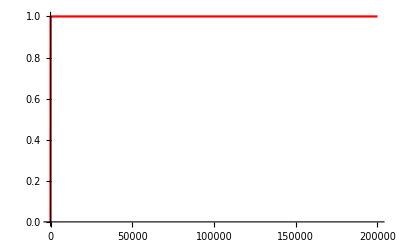

```mathematica
tmax=200000;
sol=SimulateRxnsys[crn3,tmax];Plot[Evaluate[X[t]/.sol],{t,0,tmax},PlotRange->{0,All},PlotStyle->{{Red}}]
```

```mathematica
tmax=200000;
trajectory=SimulateRxnsysSSA[crn3,tmax];
(*ListLinePlot[trajectory,PlotRange->{0,All},
PlotLegends->SpeciesInRxnsys[crn3]]*)
```

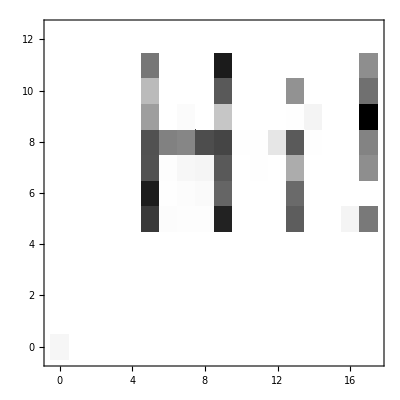

```mathematica
DensityHistogram[WeightedTrajectory[trajectory,{1,2}],{1},ColorFunction->Function[{d},GrayLevel[1-d]]]
```